```mathematica
(*Consideramos la función que se representa en la gráfica y además que corresponde a la ecuación f(x)=0*)
```

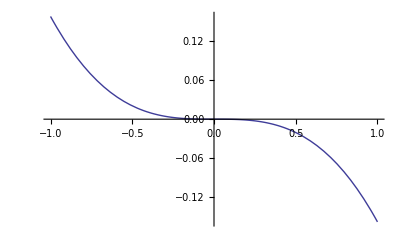

```mathematica
Plot[Sin[x]-x,{x,-1,1}]
```

```mathematica
f[x_]:=x-Sin[x]
```

```mathematica
Simplify [x-f[x]/f'[x]]
```

(x Cos[x]-Sin[x])/(-1+Cos[x])

```mathematica
(*Generamos la función de iteración para la ecuación indicada:*)
```

```mathematica
g[x_]:=(x Cos[x]-Sin[x])/(-1+Cos[x])
```

```mathematica
(*Metemos los datos iniciales y calculamos f y las tres primeras derivadas*)
```

```mathematica
x0=1.`30
f[x0]
f'[x0]
f''[x0]
f'''[x0]
```

1.

0.15852901519210349334749767837

0.45969769413186028259906339256

0.84147098480789650665250232163

0.54030230586813971740093660744

```mathematica
(*Repetimos para cada iteración*)
```

```mathematica
x1=g[x0]
ea=Abs[x1-x0]
f[x1]
f'[x1]
f''[x1]
f'''[x1]
```

0.65514507204243050849123267931

0.3448549279575694915087673207

0.0458707860408957714994116379

0.2070404522188284714478697222

0.60927428600153473699182104142

0.79295954778117152855213027775

```mathematica
x2=g[x1]
ea=Abs[x2-x1]
f[x2]
f'[x2]
f''[x2]
f'''[x2]
```

0.433590368363492953084118256

0.221554703678937555407114423

0.013458737959401029720028739

0.0925368254667303013407169284

0.420131630404091923364089517

0.9074631745332696986592830716

```mathematica
x3=g[x2]
ea=Abs[x3-x2]
f[x3]
f'[x3]
f''[x3]
f'''[x3]
```

0.2881484008925012001824382

0.14544196747099175290168005

0.00397094846041727219428052

0.041228298535459132629399026

0.28417745243208392798815769

0.958771701464540867370600974

```mathematica
x4=g[x3]
ea=Abs[x4-x3]
f[x4]
f'[x4]
f''[x4]
f'''[x4]
```

0.191832312150638927373924

0.0963160887418622728085142

0.00117439692329330877028

0.0183434616113626212396493

0.190657915227345618603649

0.9816565383886373787603507

```mathematica
x5=g[x4]
ea=Abs[x5-x4]
f[x5]
f'[x5]
f''[x5]
f'''[x5]
```

0.1278096675607081092431

0.0640226445899308181308

0.0003476843492049731648

0.00815654318043187854986

0.1274619832115031360783

0.991843456819568121450138

```mathematica
x6=g[x5]
ea=Abs[x6-x5]
f[x6]
f'[x6]
f''[x6]
f'''[x6]
```

0.08518323360286523268

0.04262643395784287657

0.0001029801567549481

0.003625898332586306553

0.08508025344611028453

0.996374101667413693447

```mathematica
x7=g[x6]
ea=Abs[x7-x6]
f[x7]
f'[x7]
f''[x7]
f'''[x7]
```

0.05678195278661749

0.02840128081624774

0.00003050771704539

0.001611661985920761

0.0567514450695721

0.998388338014079239

```mathematica
x8=g[x7]
ea=Abs[x8-x7]
f[x8]
f'[x8]
f''[x8]
f'''[x8]
```

0.03785260078111

0.01892935200551

9.0386758×10^-6

0.0007163241565578

0.03784356210531

0.9992836758434422

```mathematica
x9=g[x8]
ea=Abs[x9-x8]
f[x9]
f'[x9]
f''[x9]
f'''[x9]
```

0.0252344645

0.0126181362

2.678×10^-6

0.000318372205

0.0252317865

0.9996816277947

```mathematica
x10=g[x9]
ea=Abs[x10-x9]
f[x10]
f'[x10]
f''[x10]
f'''[x10]
```

0.016823

0.0084117

8.×10^-7

0.0001415

0.016822

0.9998585

```mathematica
x11=g[x10]
ea=Abs[x11-x10]
f[x11]
f'[x11]
f''[x11]
f'''[x11]
```

0.01

0.006

0.

0.00006

0.01

0.99994

```mathematica
(*Procedemos a considerar el método adaptado para multiplicidad 3:*)
Simplify [x-3f[x]/f'[x]]
```

(2 x+x Cos[x]-3 Sin[x])/(-1+Cos[x])

```mathematica
(*La nueva función de iteración es:*)
g[x_]:=(2 x+x Cos[x]-3 Sin[x])/(-1+Cos[x])
```

```mathematica
(*Iteración inicial:*)
x0=1.`30
```

1.

```mathematica
x1=g[x0]
ea=Abs[x1-x0]
```

-0.0345647838727084745263019621

1.034564783872708474526301962

```mathematica
x2=g[x1]
ea=Abs[x2-x1]
```

1.376571625378607366×10^-6

0.034566160444333853133667

```mathematica
x3=g[x2]
ea=Abs[x3-x2]
```

0.

1.37657×10^-6

```mathematica
(*Observa que estaríamos hablando de una aproximación en la que la primera cifra decimal no nula correspondería a la de la posición 14*)
```